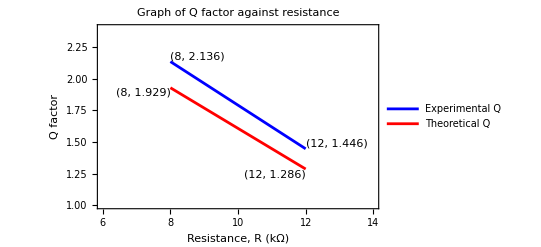

{Experimental Equation: Q = -0.17250 R + 3.520,Theoretical Equation: Q = -0.16075 R + 3.210}

```mathematica
data={{8,2.136,1.929},{12,1.446,1.286}};

ListLinePlot[{Tooltip[{#[[1]],#[[2]]},"Experimental Q"]&/@data,Tooltip[{#[[1]],#[[3]]},"Theoretical Q"]&/@data},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{"Resistance, R (kΩ)","Q factor"},PlotLegends->{"Experimental Q","Theoretical Q"},Epilog->{Text["("<>ToString[#[[1]]]<>", "<>ToString[#[[2]]]<>")",{#[[1]],#[[2]]},{-0.5,-2.0}]&/@data,Text["("<>ToString[#[[1]]]<>", "<>ToString[#[[3]]]<>")",{#[[1]],#[[3]]},{0.5,2.0}]&/@data},PlotLabel->"Graph of Q factor against resistance",PlotRange->{{6,14},{1.0,2.4}}]

(*Extract coordinates*)
experimentalQ={#[[1]],#[[2]]}&/@data;
theoreticalQ={#[[1]],#[[3]]}&/@data;

(*Calculate slope and y-intercept for each line*)
experimentalLine=Fit[experimentalQ,{1,x},x];
theoreticalLine=Fit[theoreticalQ,{1,x},x];

(*Extract slope and y-intercept for each line*)
experimentalSlope=Coefficient[experimentalLine,x];
experimentalYIntercept=experimentalLine/. x->0;

theoreticalSlope=Coefficient[theoreticalLine,x];
theoreticalYIntercept=theoreticalLine/. x->0;

(*Display the results in the form Y=mX+c with 3 decimal places*)
experimentalEquation=StringForm["Experimental Equation: Q = `` R + ``",NumberForm[experimentalSlope,{5,5}],NumberForm[experimentalYIntercept,{3,3}]];

theoreticalEquation=StringForm["Theoretical Equation: Q = `` R + ``",NumberForm[theoreticalSlope,{5,5}],NumberForm[theoreticalYIntercept,{3,3}]];

{experimentalEquation,theoreticalEquation}
```